# Space Curves and Sentiments about the Human Experience

Emmy Blumenthal

### Some vague sentiments about the human experience

We all take curved, erratic paths through life. What remains constant is that each experience is continuous from one moment to the next. The curves we take through life are dyed by how quickly our experiences change.

Complexity is a mysterious element of life. Following the ideas of A New Kind of Science, complexity emerges from simple ideas, simple iterations, and simple routines. The complex nature of life emerges from routines, small actions, words.

To express these sentiments, I will construct figures—space curves—whose properties and appearance, in a more poetic sense, reflect how complexity emerges from more simple elements and how the human experience can vary across people and across time.

### Applying math to these sentiments

Let’s begin with a simple expression. Call it term 0.

1

We’ll add a little imagination and progress by a step. Term 1.

ⅈ x

And another step. Term 2.

-1/2 x^2

And some more steps. Term 3, 4, and 5.

-1/6ⅈx^3

1/24 x^4

ⅈ/120 x^5

Each term is evolved one step at a time. Call the nth term a_n. a_n progress according to a simple rule.

a_(n+1)=ⅈ 1/(n+1)x  a_n

Let’s see what a_n is generally.

```mathematica
a[n_]=RSolveValue[{a[n+1]==(I x)/(n+1) a[n],a[0]==1},a[n],n]
```

(ⅈ x)^n/Pochhammer[2,-1+n]

This can also be written as

a_n = 1/(n!)(ⅈ x)^n

And to check:

```mathematica
FullSimplify[a[n]==(I x)^n/(n!)]
```

True

This is a simple process. Now, let’s add another simple element. Let’s sum.

```mathematica
Sum[a[n],{n,0,5}]
```

1+ⅈ x-x^2/2-(ⅈ x^3)/6+x^4/24+(ⅈ x^5)/120

a_0+a_1+a_2+a_3+a_4+a_5=1+ⅈ x-x^2/2-(ⅈ x^3)/6+x^4/24+(ⅈ x^5)/120

Again we can iterate. To infinity.

∑_(n=0)^∞ a_n

This complex (a pun) function is simply the product of iteration of smaller, simpler expressions. This function is simply

ⅇ^(ⅈ t)

We can visualize the curve as the parameter t varies:

```mathematica
Manipulate[ParametricPlot[ReIm[Exp[I t]],{t,0,tf},PlotRange->1.1],{{tf,π/3,""},0.01,2π}]
```

Again, let’s come up with a simple transformation, and we’ll apply it to this curve. We’ll scale the radius of the curve and the rate at which the curve progresses around the origin. This transformation takes the simple form.

b ⅇ^(a ⅈ t)

What should we choose as for the constants a and b? We will choose these at random from something that also emerges after many simple steps. As dictated by the central limit theorem, the normal distribution arises when independent variables are summed together. The variables a and b will be distributed independently according to the normal distribution. We can plot, on the complex plane, ten different variates of this curve.

```mathematica
(#1Exp[I#2 t]&@@RandomVariate[NormalDistribution[],{2,10}]);
Manipulate[ParametricPlot[Evaluate[ReIm/@%],],]
```

Next, we can perform one more elementary operation and add these different curves.

b_1 ⅇ^(a_1 ⅈ t)+b_2 ⅇ^(a_2 ⅈ t)+b_3 ⅇ^(a_3 ⅈ t)+⋯

In return, we get a beautiful smooth but complex and unique curve.

```mathematica
f=Plus@@(#1Exp[I#2 t]&@@RandomVariate[NormalDistribution[],{2,10}]);
Animate[ParametricPlot[ReIm@f,],]
```

These curves seem to be almost unpredictable in how they will turn and twist. The human experience is unpredictable. Each moment seems Let’s highlight when the curve curves the most. Curvature is defined for a parametric curve {x(t),y(t)} to be

κ=(|x'(t)y''(t)-y'(t)x''(t)|)/((x'(t)^2+y'(t)^2)^(3/2))

where, for us, x  = Re(our curve) and y  = Im(our curve). We can see how this curvature varies over life

```mathematica
f//TraditionalForm
```

-1.45585 ⅇ^((0.+0.266446 ⅈ) t)+1.07417 ⅇ^((0.+0.476504 ⅈ) t)+0.639172 ⅇ^((0.+0.793801 ⅈ) t)+0.129054 ⅇ^((0.+1.01664 ⅈ) t)+0.300531 ⅇ^((0.-1.38315 ⅈ) t)+1.56199 ⅇ^((0.+1.68906 ⅈ) t)+0.650652 ⅇ^((0.-1.69912 ⅈ) t)+1.70311 ⅇ^((0.+1.95006 ⅈ) t)+0.742234 ⅇ^((0.+2.49101 ⅈ) t)+1.09743 ⅇ^((0.-2.64194 ⅈ) t)

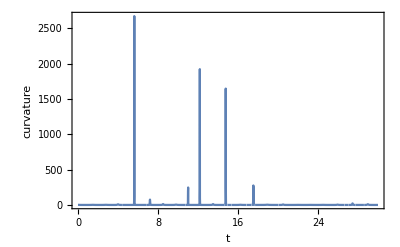

```mathematica
fxp=D[ComplexExpand[Re[f]],t];
fyp=D[ComplexExpand[Im[f]],t];
fxpp=D[ComplexExpand[Re[f]],t,t];
fypp=D[ComplexExpand[Im[f]],t,t];
curv=RealAbs[fxp fypp -fyp fxpp]/((fxp^2+fyp^2)^(3/2));
Plot[curv,]
```

Life changes and curves more dramatically at some points more than at others. We can finally plot a variety of these curves at different lengths—representing different ages within the human experience. We’ll visualize the curvature of these curves using a color function.

```mathematica
ColorData["FuchsiaTones"]
```

ColorDataFunction[…]

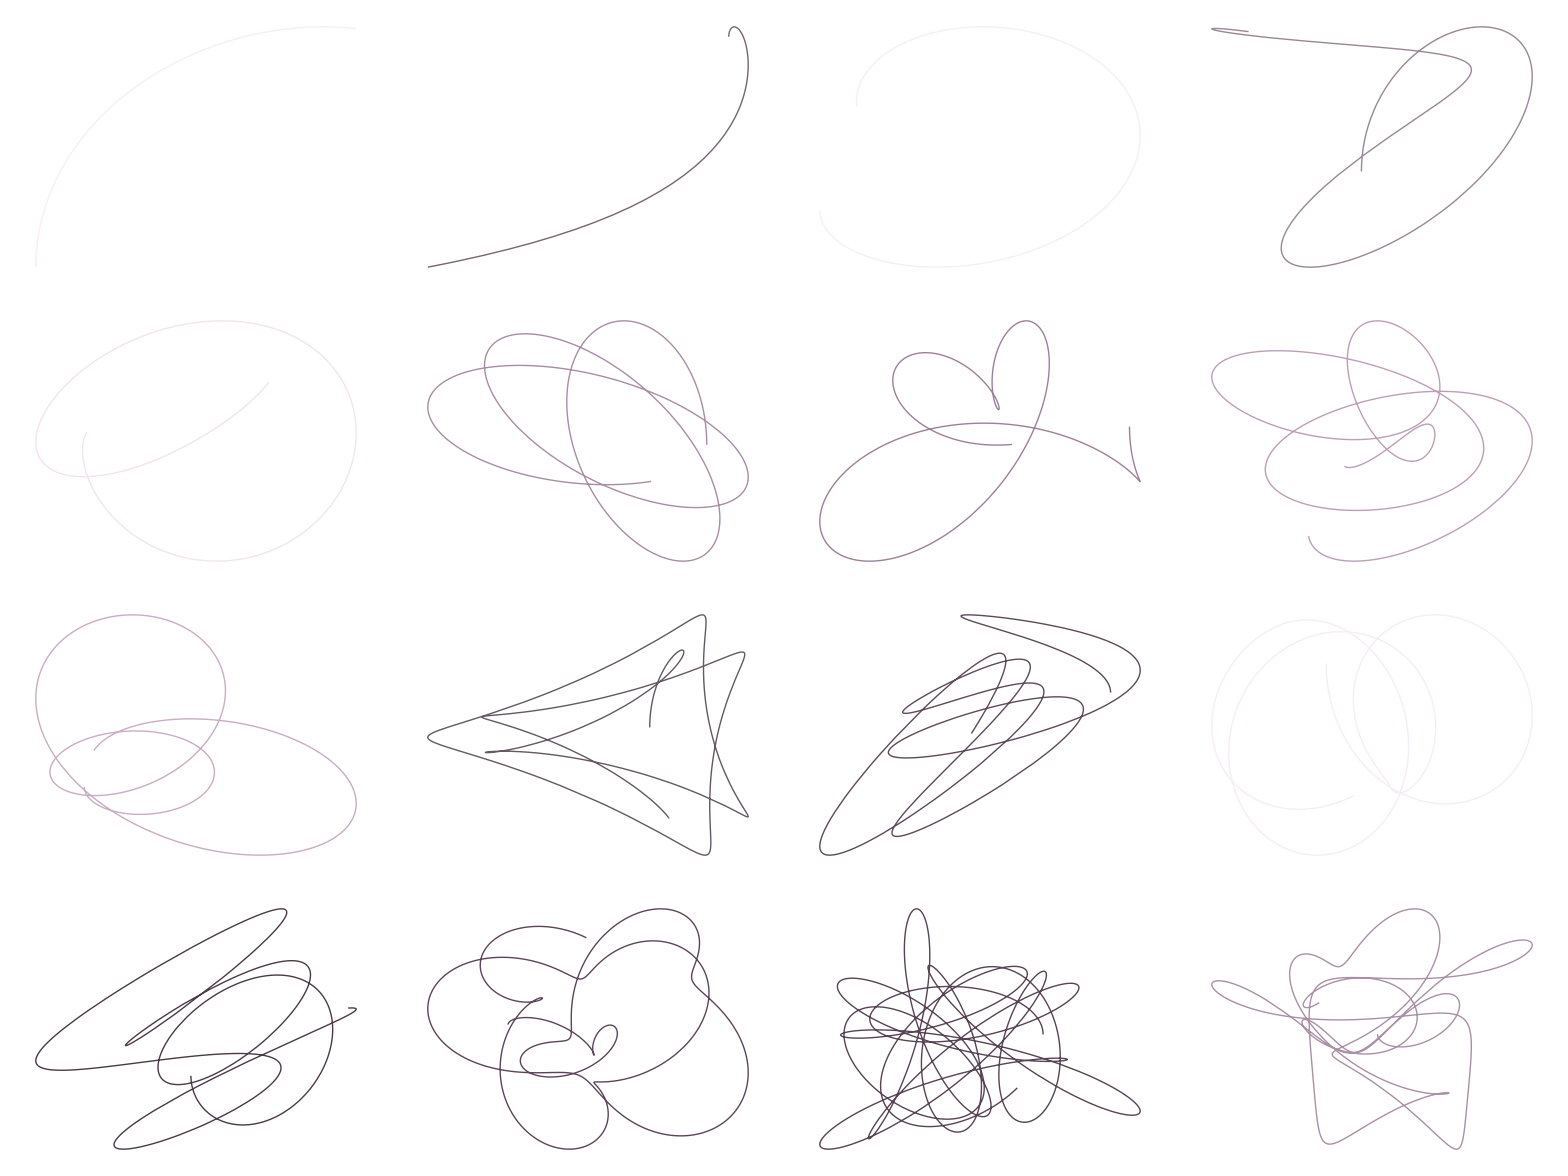

```mathematica
Grid[Partition[Table[Module[{f=Plus@@(#1Exp[I#2 t]&@@RandomVariate[NormalDistribution[],{2,10}])},
fxp=D[ComplexExpand[Re[f]],t];
fyp=D[ComplexExpand[Im[f]],t];
fxpp=D[ComplexExpand[Re[f]],t,t];
fypp=D[ComplexExpand[Im[f]],t,t];
curv=RealAbs[fxp fypp -fyp fxpp]/((fxp^2+fyp^2)^(3/2));
max=First@Quiet@FindMaximum[{curv,0≤t≤tf},{t,tf/2}];
min=First@Quiet@FindMinimum[{curv,0≤t≤tf},{t,tf/2}];
ParametricPlot[ReIm[f],{t,0,tf},]],{tf,1,32,2}],4]]
```

These beautiful, unique curves are reflective of varying life experiences.
Sometimes we have dramatic turning points that shape our lives. Sometimes, life changes direction more slowly. Our experiences are dyed, colored, and shaped by the curvature of our experience. 
As we progress through life, we take these erratic paths, but we will all orbit around some center, our core values—who we are.